```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\analysis-mirror_neutrons\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures\\nstar\\runs2"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/analysis-mirror_neutrons/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar/runs"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metaStructure2={Number,Number,Number,Number,Number,Number,Number,Word,Real};
metaStructure3={Real,Real,Real,Real,Real,Real,Real};
descdat=ReadList[StringJoin[descDir,seperator,"desc3.dat"],metaStructure2];
metalvl3={Real,Real,Real,Real,Real,Real,Real,Real};
ts={35,50,65,80,95,110,125,140,155,170,180,200,215,220,230,240,245,260,275,280,290,300,305,320,335,340,350,360,365,380};
tssz=Dimensions[ts][[1]];
tsadd=PlusMinus[11.3,0.397];
(*Print["Executing: ts = ",ts[[i]]," , i = ",i];*)
tfal=ReadList[StringJoin[descDir,seperator,"tf-Al.dat"],metaStructure3];
tfcu=ReadList[StringJoin[descDir,seperator,"tf-Cu.dat"],metaStructure3];
tk2[l_,u_,a_,b_,c_,d_,int_]:=SetPrecision[N[Table[{10^j,Superscript["10",j],{a,b}},{j,l,u,int}]~Join~Table[{10^j,"",{c,d}},{j,l-N[Log10[2]],u+N[Log10[2]],int}]],3];
pttfmual=Table[{{tfal[[k]][[1]],2tsadd[[2]]},{tfal[[k]][[2]],tfal[[k]][[4]]}},{k,1,tssz}];
pttfmucu=Table[{{tfcu[[k]][[1]],2tsadd[[2]]},{tfcu[[k]][[2]],tfcu[[k]][[4]]}},{k,1,tssz}];
pttf2mual=Table[{{tfal[[k]][[1]],2tsadd[[2]]},{tfal[[k]][[5]],tfal[[k]][[7]]}},{k,1,tssz}];
pttf2mucu=Table[{{tfcu[[k]][[1]],2tsadd[[2]]},{tfcu[[k]][[5]],tfcu[[k]][[7]]}},{k,1,tssz}];
```

Working Directory: C:\Users\tmpra\Dropbox\nEDM\analysis-mirror_neutrons\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\runs2

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

```mathematica
i=16;
lvl3=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3.dat"],metalvl3];
maxsz=1000;
maxsz3=1000;
(*maxsz2=100000;*)
tf=Table[0,{k,1,maxsz}];
tf2tf=Table[0,{k,1,maxsz}];
If[i≤15,
kk=Position[tfal,descdat[[i]][[7]]+2*tsadd[[1]]][[1]][[1]];
tf=RandomVariate[NormalDistribution[tfal[[kk]][[2]],tfal[[kk]][[4]]],maxsz];
tf2tf=RandomVariate[NormalDistribution[tfal[[kk]][[5]],tfal[[kk]][[7]]],maxsz];
,
kk=Position[tfcu,descdat[[i]][[7]]+2*tsadd[[1]]][[1]][[1]];
tf=RandomVariate[NormalDistribution[tfcu[[kk]][[2]],tfcu[[kk]][[4]]],maxsz];
tf2tf=RandomVariate[NormalDistribution[tfcu[[kk]][[5]],tfcu[[kk]][[7]]],maxsz];
];
(***)
ab=RandomVariate[NormalDistribution[lvl3[[1]][[1]],lvl3[[1]][[2]]],maxsz3];
eb=RandomVariate[NormalDistribution[lvl3[[1]][[3]],lvl3[[1]][[4]]],maxsz3];
tftseb0=Flatten[KroneckerProduct[1/eb,(descdat[[i]][[7]]+2tsadd[[1]])*tf2tf]];
tftsab=Flatten[KroneckerProduct[1/ab,(descdat[[i]][[7]]+2tsadd[[1]])/tf]];
tftseb=Flatten[KroneckerProduct[1/eb,(descdat[[i]][[7]]+2tsadd[[1]])/tf]];
```

## A

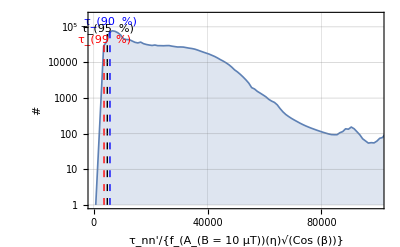

```mathematica
histlst=HistogramList[3*Sqrt[tftsab]];
hstbl=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+ histlst[[1]][[k]],histlst[[2]][[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
fthst=Fit[hstbl,Table[x^k,{k,0,20,1}],x];
fthst2=Interpolation[hstbl,InterpolationOrder->2];
estbckp=EstimatedBackground[hstbl[[;;,2]],10,Method->{"SNIP",10}];
estbckm=-EstimatedBackground[-hstbl[[;;,2]],10,Method->{"SNIP",10}];
estbckm2=-EstimatedBackground[-estbckm,10,Method->{"SNIP",10}];
ptbckp=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckp[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
ptbckm=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckm[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
ptbckm2=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckm2[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
histhisttftseb0tot=Total[estbckm2];
cumhisttftseb0t=ParallelTable[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],Total[estbckm2[[;;k]]]/histhisttftseb0tot},{k,1,Dimensions[histlst][[1]]}];
val90=Nearest[cumhisttftseb0t[[;;,2]],0.1][[1]];
val95=Nearest[cumhisttftseb0t[[;;,2]],0.05][[1]];
val99=Nearest[cumhisttftseb0t[[;;,2]],0.01][[1]];
(**************************)
lineStyle1={Thick,Dashed,Blue};
lineStyle2={Thick,Dashed,Black};
lineStyle3={Thick,Dashed,Red};
line1=Line[{{5716,Log@(10^0)},{5716,Log@(10^5.05)}}];
line2=Line[{{4783,Log@(10^0)},{4783,Log@(10^4.8)}}];
line3=Line[{{3634,Log@(10^0)},{3634,Log@(10^4.5)}}];
adat10=Join[Table[{10k,.1},{k,0,10}],(ptbckm+hstbl)/2];
ListLinePlot[{adat10},Frame->True,FrameLabel->{"τ_nn'/{f_(A_(B = 10  μT))(η)√(Cos (β))}","#"},PlotRange->{{1,99999},{1,2*10^5}},PlotStyle->Thickness[.003],Filling->{1->Axis},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{5716,Log@(10^5.15)}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{4783,Log@(10^4.95)}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{3634,Log@(10^4.65)}],Large]}
}]
```

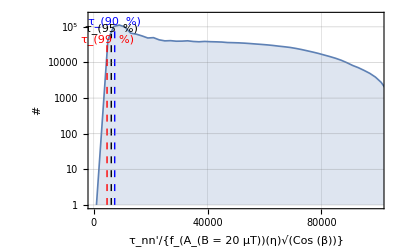

```mathematica
histlst=HistogramList[3.75*Sqrt[tftsab]];
hstbl=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+ histlst[[1]][[k]],histlst[[2]][[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
fthst=Fit[hstbl,Table[x^k,{k,0,20,1}],x];
fthst2=Interpolation[hstbl,InterpolationOrder->2];
estbckp=EstimatedBackground[hstbl[[;;,2]],10,Method->{"SNIP",10}];
estbckm=-EstimatedBackground[-hstbl[[;;,2]],10,Method->{"SNIP",10}];
estbckm2=-EstimatedBackground[-estbckm,10,Method->{"SNIP",10}];
ptbckp=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckp[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
ptbckm=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckm[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
ptbckm2=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckm2[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
histhisttftseb0tot=Total[estbckm2];
cumhisttftseb0t=ParallelTable[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],Total[estbckm2[[;;k]]]/histhisttftseb0tot},{k,1,Dimensions[histlst][[1]]}];
val90=Nearest[cumhisttftseb0t[[;;,2]],0.1][[1]];
val95=Nearest[cumhisttftseb0t[[;;,2]],0.05][[1]];
val99=Nearest[cumhisttftseb0t[[;;,2]],0.01][[1]];
(**************************)
lineStyle1={Thick,Dashed,Blue};
lineStyle2={Thick,Dashed,Black};
lineStyle3={Thick,Dashed,Red};
line1=Line[{{7383,Log@(10^0)},{7383,Log@(10^5.05)}}];
line2=Line[{{6178,Log@(10^0)},{6178,Log@(10^4.8)}}];
line3=Line[{{4693,Log@(10^0)},{4693,Log@(10^4.5)}}];
adat20=Join[Table[{10k,.1},{k,0,10}],(ptbckm+hstbl)/2];
ListLinePlot[{adat20},Frame->True,FrameLabel->{"τ_nn'/{f_(A_(B = 20  μT))(η)√(Cos (β))}","#"},PlotRange->{{1,99999},{1,2*10^5}},PlotStyle->Thickness[.003],Filling->{1->Axis},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{7383,Log@(10^5.15)}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{6178,Log@(10^4.95)}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{4693,Log@(10^4.65)}],Large]}
}]
```

```mathematica
(*PRL/D*)
```

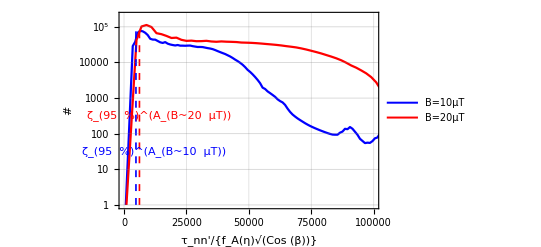

```mathematica
lineStyle3={Thickness[.003],Dashed,Red};
lineStyle1={Thickness[.003],Dashed,Blue};
line210=Line[{{6178,Log@(10^0)},{6178,Log@(10^5.05)}}];
line220=Line[{{4783,Log@(10^0)},{4783,Log@(10^5.05)}}];
ListLinePlot[{adat10,adat20},Frame->True,FrameLabel->{"τ_nn'/{f_A(η)√(Cos (β))}","#"},PlotRange->{{1,99999},{1,2*10^5}},PlotStyle->{{Blue,Thickness[.004]},{Red,Thickness[.004]}},PlotLegends->{"B=10μT","B=20μT"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thickness[.005],FrameStyle->Thickness[.005],ImageSize->{1200},
Epilog->{
{Directive[lineStyle3],line210,Style[Text["ζ_(95  %)^(A_(B~20  μT))",{14000,Log@(10^2.5)}],{FontSize->48,Bold}]},
{Directive[lineStyle1],line220,Style[Text["ζ_(95  %)^(A_(B~10  μT))",{12000,Log@(10^1.5)}],{FontSize->48,Bold}]}
}]
```

## E

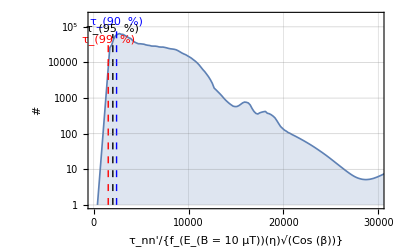

```mathematica
histlst=HistogramList[1.55Sqrt[tftseb]];
hstbl=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+ histlst[[1]][[k]],histlst[[2]][[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
fthst=Fit[hstbl,Table[x^k,{k,0,20,1}],x];
fthst2=Interpolation[hstbl,InterpolationOrder->2];
estbckp=EstimatedBackground[hstbl[[;;,2]],10,Method->{"SNIP",10}];
estbckm=-EstimatedBackground[-hstbl[[;;,2]],10,Method->{"SNIP",10}];
estbckm2=-EstimatedBackground[-estbckm,10,Method->{"SNIP",10}];
ptbckp=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckp[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
ptbckm=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckm[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
ptbckm2=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckm2[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
histhisttftseb0tot=Total[estbckm2];
cumhisttftseb0t=ParallelTable[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],Total[estbckm2[[;;k]]]/histhisttftseb0tot},{k,1,Dimensions[histlst][[1]]}];
val90=Nearest[cumhisttftseb0t[[;;,2]],0.1][[1]];
val95=Nearest[cumhisttftseb0t[[;;,2]],0.05][[1]];
val99=Nearest[cumhisttftseb0t[[;;,2]],0.01][[1]];
(***********************)
lineStyle1={Thick,Dashed,Blue};
lineStyle2={Thick,Dashed,Black};
lineStyle3={Thick,Dashed,Red};
line1=Line[{{2412,Log@(10^0)},{2412,Log@(10^5.05)}}];
line2=Line[{{2018,Log@(10^0)},{2018,Log@(10^4.8)}}];
line3=Line[{{1533,Log@(10^0)},{1533,Log@(10^4.5)}}];
edat10=Join[Table[{10k,.1},{k,0,10}],(ptbckm+hstbl)/2];
ListLinePlot[{edat10},Frame->True,FrameLabel->{"τ_nn'/{f_(E_(B = 10  μT))(η)√(Cos (β))}","#"},PlotRange->{{1,29999},{1,2*10^5}},PlotStyle->Thickness[.003],Filling->{1->Axis},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{2412,Log@(10^5.15)}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{2018,Log@(10^4.95)}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{1533,Log@(10^4.65)}],Large]}
}]
```

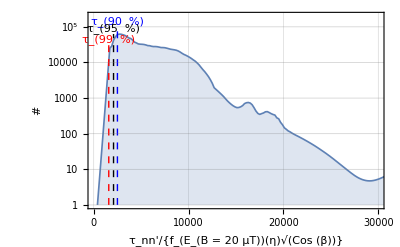

```mathematica
histlst=HistogramList[1.575*Sqrt[tftseb]];
hstbl=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+ histlst[[1]][[k]],histlst[[2]][[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
fthst=Fit[hstbl,Table[x^k,{k,0,20,1}],x];
fthst2=Interpolation[hstbl,InterpolationOrder->2];
estbckp=EstimatedBackground[hstbl[[;;,2]],10,Method->{"SNIP",10}];
estbckm=-EstimatedBackground[-hstbl[[;;,2]],10,Method->{"SNIP",10}];
estbckm2=-EstimatedBackground[-estbckm,10,Method->{"SNIP",10}];
ptbckp=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckp[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
ptbckm=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckm[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
ptbckm2=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckm2[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
histhisttftseb0tot=Total[estbckm2];
cumhisttftseb0t=ParallelTable[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],Total[estbckm2[[;;k]]]/histhisttftseb0tot},{k,1,Dimensions[histlst][[1]]}];
val90=Nearest[cumhisttftseb0t[[;;,2]],0.1][[1]];
val95=Nearest[cumhisttftseb0t[[;;,2]],0.05][[1]];
val99=Nearest[cumhisttftseb0t[[;;,2]],0.01][[1]];
(***********************)
lineStyle1={Thick,Dashed,Blue};
lineStyle2={Thick,Dashed,Black};
lineStyle3={Thick,Dashed,Red};
line1=Line[{{2502,Log@(10^0)},{2502,Log@(10^5.05)}}];
line2=Line[{{2093,Log@(10^0)},{2093,Log@(10^4.8)}}];
line3=Line[{{1590,Log@(10^0)},{1590,Log@(10^4.5)}}];
edat20=Join[Table[{10k,.1},{k,0,10}],(ptbckm+hstbl)/2];
ListLinePlot[{edat20},Frame->True,FrameLabel->{"τ_nn'/{f_(E_(B = 20  μT))(η)√(Cos (β))}","#"},PlotRange->{{1,29999},{1,2*10^5}},PlotStyle->Thickness[.003],Filling->{1->Axis},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{2502,Log@(10^5.15)}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{2093,Log@(10^4.95)}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{1590,Log@(10^4.65)}],Large]}
}]
```

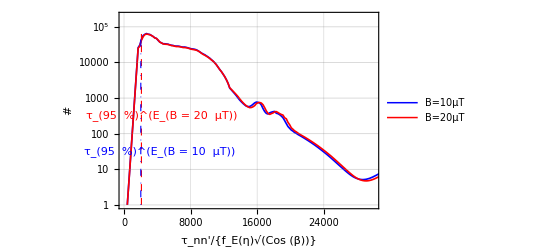

```mathematica
lineStyle3={Thickness[.002],Dashed,Red};
lineStyle1={Thickness[.002],DotDashed,Blue};
line220=Line[{{2018,Log@(10^0)},{2018,Log@(10^4.8)}}];
line210=Line[{{2093,Log@(10^0)},{2093,Log@(10^4.8)}}];
ListLinePlot[{edat10,edat20},Frame->True,FrameLabel->{"τ_nn'/{f_E(η)√(Cos (β))}","#"},PlotRange->{{1,29999},{1,2*10^5}},PlotStyle->{{Blue,Thickness[.003]},{Red,Thickness[.003]}},PlotLegends->{"B=10μT","B=20μT"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thickness[.005],FrameStyle->Thickness[.005],ImageSize->{1200},
Epilog->{
{Directive[lineStyle3],line210,Style[Text["τ_(95  %)^(E_(B = 20  μT))",{4500,Log@(10^2.5)}],{FontSize->48,Bold}]},
{Directive[lineStyle1],line220,Style[Text["τ_(95  %)^(E_(B = 10  μT))",{4250,Log@(10^1.5)}],{FontSize->48,Bold}]}
}]
```